№1

```mathematica
F={0.1, 0.2,0.3,0.4};
```

```mathematica
Perem={1.912, -2.578, 6.870, -9.497};
```

```mathematica
n=Length[F]-1;
```

```mathematica
Do[{Subscript[x, i]=F[[i+1]],Subscript[y, i]=Perem[[i+1]]},{i,0,n}]
```

```mathematica
e=1/2*10^-3;
```

```mathematica
m1=1;
```

```mathematica
m2=2;
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m1}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m1}];
```

```mathematica
eqv=Table[∑_(i=0)^m1 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m1}]
```

{4. a_0+1. a_1==-3.293,1. a_0+0.3 a_1==-2.0622}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m1 Subscript[a, i]*x^i)/.Koef
```

5.3715-24.779 x

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m1}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

5.3715-24.779 x

```mathematica
P[x]==P1[x]
```

True

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

5.34511

```mathematica
γ<e
```

False

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

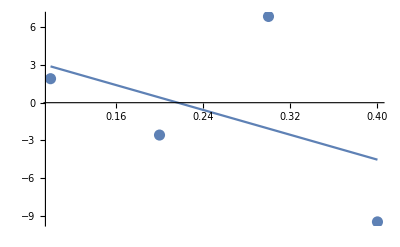

```mathematica
Show[Gr1,Gr2]
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m2}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m2}];
```

```mathematica
eqv=Table[∑_(i=0)^m2 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m2}]
```

{4. a_0+1. a_1+0.3 a_2==-3.293,1. a_0+0.3 a_1+0.1 a_2==-2.0622,0.3 a_0+0.1 a_1+0.0354 a_2==-0.98522}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m2 Subscript[a, i]*x^i)/.Koef
```

-9.47475+123.683 x-296.925 x^2

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m2}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

-9.47475+123.683 x-296.925 x^2

```mathematica
P[x]==P1[x]
```

-9.47475+123.683 x-296.925 x^2==-9.47475+123.683 x-296.925 x^2

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

4.44452

```mathematica
γ<e
```

False

```mathematica
k1=γ/e
```

8889.04

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

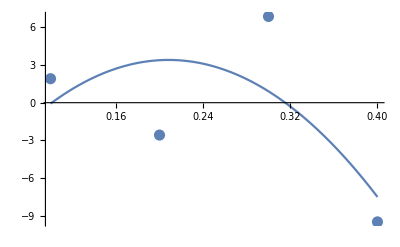

```mathematica
Show[Gr1,Gr2]
```

№2

```mathematica
m3=3;
```

```mathematica
Do[Subscript[t, i]=∑_(k=0)^n Subscript[x, k]^i,{i,0,2m3}];
```

```mathematica
Do[ Subscript[c, i]=∑_(k=0)^n Subscript[y, k] Subscript[x, k]^i,{ i,0,m3}];
```

```mathematica
eqv=Table[∑_(i=0)^m3 Subscript[a, i] Subscript[t, i+k]==Subscript[c, k],{k,0,m3}]
```

{4. a_0+1. a_1+0.3 a_2+0.1 a_3==-3.293,1. a_0+0.3 a_1+0.1 a_2+0.0354 a_3==-2.0622,0.3 a_0+0.1 a_1+0.0354 a_2+0.013 a_3==-0.98522,0.1 a_0+0.0354 a_1+0.013 a_2+0.00489 a_3==-0.44103}

```mathematica
Koef=Solve[eqv,{}]//Flatten;
```

```mathematica
P[x_]=(∑_(i=0)^m3 Subscript[a, i]*x^i)/.Koef
```

60.093-982.775 x+4672.2 x^2-6625.5 x^3

```mathematica
Tbl=Table[{Subscript[x, k],Subscript[y, k]},{k,0,n}];
```

```mathematica
Fun=Table[x^i,{i,0,m3}];
```

```mathematica
P1[x_]=Fit[Tbl,Fun,x]
```

60.093-982.775 x+4672.2 x^2-6625.5 x^3

```mathematica
(P[x]-P1[x])//Chop
```

-1.26505×10^-10+1.97178×10^-9 x-8.69659×10^-9 x^2+1.14314×10^-8 x^3

```mathematica
γ=√(1/(n+1)*∑_(k=0)^n (P[Subscript[x, k]]-Subscript[y, k])^2)//N
```

7.76509×10^-12

```mathematica
k2=e/γ
```

6.43907×10^7

```mathematica
If[k1<k2,opt=2,3]
```

2

```mathematica
Gr1=ListPlot[Tbl,PlotStyle->{PointSize[0.02]}];
```

```mathematica
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
```

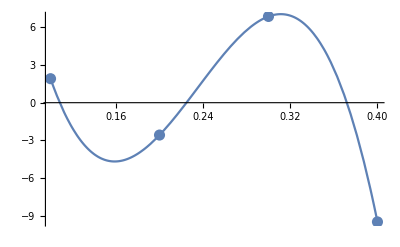

```mathematica
Show[Gr1,Gr2]
```